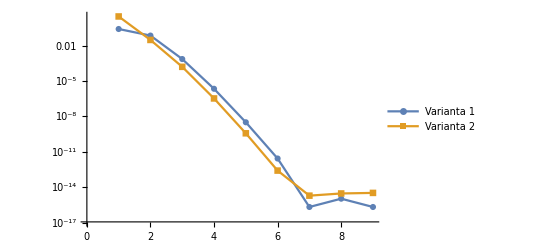

```mathematica
Remove["Global`*"]
(*Maximální řád kvadratury*)
d=9;

(*Integrovaná funkce*)
fun1[x_,y_]=x^2 Exp[x];

(*Trojúhelník přes který se integruje*)
vrchol1={0,0};
vrchol2={1,0};
vrchol3={0,1};
verticesPoints={vrchol1,vrchol2,vrchol3};

(*Definice trojúhelníku*)
triangle=Triangle[verticesPoints];

(*Plocha trojúhelníku*)
area=RegionMeasure[triangle];

(*Určení uzlů v jedné dimenzi pro jednotlivé řády kvadratury*)
solutionSolve=Table[Solve[LegendreP[n,x]==0],{n,1,d}];
solution=Table[x/.solutionSolve[[n]][[i]],{n,1,d},{i,1,n}];

(*Váhy pro jednotlivé řády kvadratury*)
weights=Table[2/((1-solution[[n]][[i]]^2)((D[LegendreP[n,x],x]/.solutionSolve[[n]][[i]])^2)),{n,1,d},{i,1,Length[solutionSolve[[n]]]}];

(*Součinové pravidlo Varianta 1 aplikované na funkci fun1 pro řády kvadratury 1 až d*)
sumTable=Table[weights[[n]][[i]](1-solution[[n]][[i]])Total[Table[weights[[n]][[j]] fun1[(1+solution[[n]][[i]])/2,((1-solution[[n]][[i]])(1+solution[[n]][[j]]))/4],{j,1,n}]],{n,1,d},{i,1,n}];
gaussNesym=Table[N[(area/4)Total[sumTable[[n]]]],{n,1,d}];

(*Přesný integrál*)
exactIntegral=N[Integrate[fun1[x,y],{x,y}∈triangle]];

(*Chyba kvadratury Varianta 1*)
error1=Table[N[Abs[Abs[gaussNesym[[n]]-exactIntegral]/gaussNesym[[n]]]],{n,1,d}];

(*Součinové pravidlo Varianta 2 aplikované na funkci fun1 pro řády kvadratury 1 až d*)
sumTable1=Table[weights[[n]][[i]](1-solution[[n]][[i]])Total[Table[weights[[n]][[j]] fun1[((1-solution[[n]][[i]])(1+solution[[n]][[j]]))/4,(1+solution[[n]][[i]])/2],{j,1,n}]],{n,1,d},{i,1,n}];
gaussNesym=Table[N[(area/4)Total[sumTable1[[n]]]],{n,1,d}];

(*Chyba kvadratury Varianta 2*)
error2=Table[N[Abs[Abs[gaussNesym[[n]]-exactIntegral]/gaussNesym[[n]]]],{n,1,d}];

(*Srování Varianty 1 a Varianty 2*)
graph1=Table[{n,$MachineEpsilon+error1[[n]]},{n,1,d}];
graph2=Table[{n,$MachineEpsilon+error2[[n]]},{n,1,d}];
graphic=ListLinePlot[{graph1,graph2},ScalingFunctions->{"Linear","Log"},PlotMarkers->Automatic,Joined->True,PlotLegends->{"Varianta 1","Varianta 2"}]
```